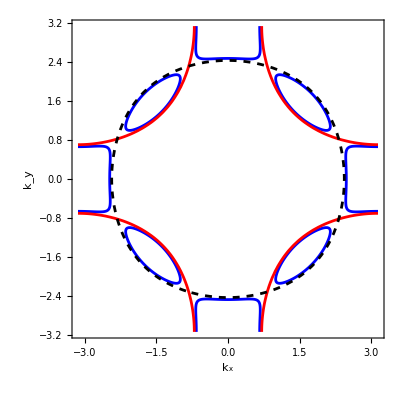

doping p:

-0.00751149

ρ_c:

0.503756

ρ_f:

0.503756

```mathematica
μc=-0.74;
tc=1;
tc1=-0.4;
tc2=0;
tc3=0;
c=4;
L=11;
ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=ekc/.kx->kx+π/.ky->ky+π;
m=0.3;
(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+m^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+m^2);
δ=0.01;
Ac=-1/π Im[(ω-ekf+ⅈ δ)/((ω-ekf+ⅈ δ)(ω-ekc+ⅈ δ)-m^2)];
enlevel=0;
Show[ContourPlot[{E1==enlevel,E2==enlevel,ekc==enlevel,ekf==enlevel},{kx,-π,π},{ky,-π,π},ContourStyle->{Blue,Blue,{Red},{Black,Dashed}},LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)","\!\(\*SubscriptBox[\(k\), \(y\)]\)"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None},{All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,MaxRecursion->3]]
T=8.61 10^-5 40;

nf[x_]:=1/(1+Exp[x/T]);
Text["doping p:"]
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
1-2ρc

Text["ρ_c:"]
ρc
Text["ρ_f:"]
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]
```

```mathematica
Plot3D[{ekc,0},{kx,-π,π},{ky,-π,π}]
```

-Graphics3D-

```mathematica
Plot3D[{E1,E2,0},{kx,-π,π},{ky,-π,π}]
```

-Graphics3D-

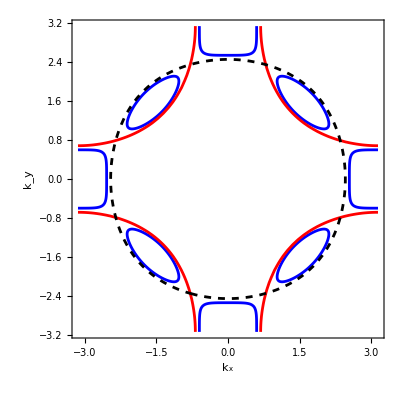
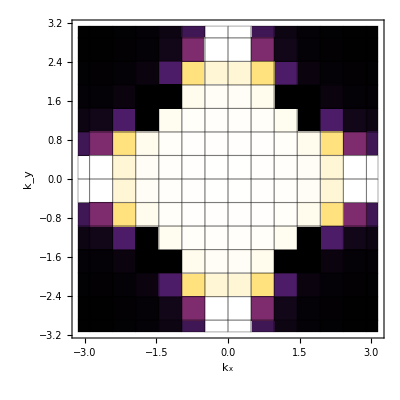

General::munfl: 0.9986 1.25356956891×10^-801 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.998425 1.026736205×10^-749 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.997728 6.21694084315×10^-606 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

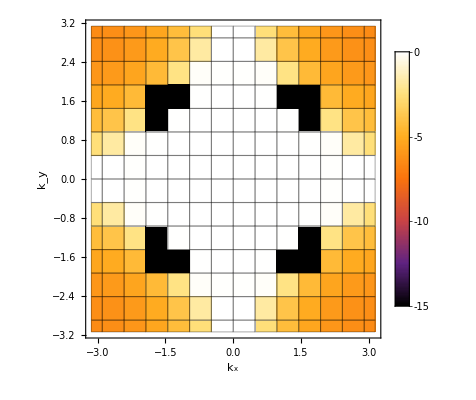

```mathematica
ListDensityPlot[Flatten[Table[{kx,ky,Log[Evaluate[((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2])]]},{kx,-π,π,2 π/13},{ky,-π,π,2 π/13}],1],ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotLegends->Automatic,ClippingStyle->Automatic]
```

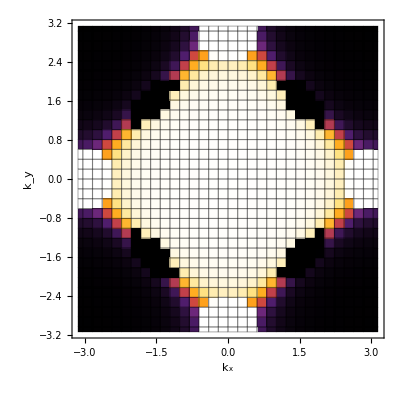

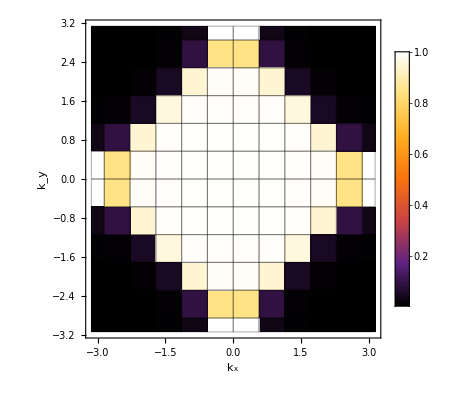
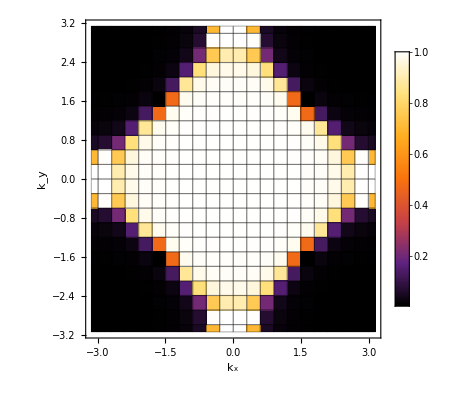
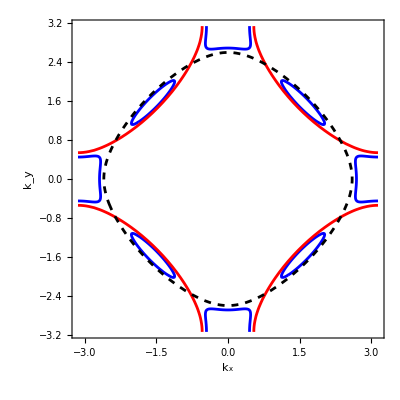

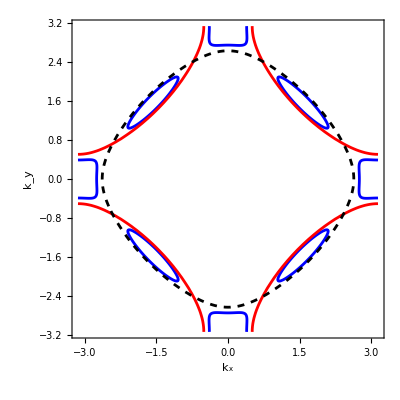

doping p:

-5.98412×10^-6

ρ_c:

0.500003

ρ_f:

0.500003

```mathematica
μc=-0.448;
tc=1;
tc1=-0.2;
tc2=0;
tc3=0;
c=4;
L=48;
ekc=-2 tc(Cos[kx]+Cos[ky])-4(tc1)Cos[kx]Cos[ky]-2 tc2(Cos[2kx]+Cos[2ky])-4tc3(Cos[2kx]Cos[ky]+Cos[kx] Cos[2ky])-μc;
ekf=ekc/.kx->kx+π/.ky->ky+π;
m=0.25;
(*hybridized bands*)
E1=(ekc+ekf)/2+√(((ekc-ekf)/2)^2+m^2);
E2=(ekc+ekf)/2-√(((ekc-ekf)/2)^2+m^2);
δ=0.01;
Ac=-1/π Im[(ω-ekf+ⅈ δ)/((ω-ekf+ⅈ δ)(ω-ekc+ⅈ δ)-m^2)];
enlevel=0;
Show[ContourPlot[{E1==enlevel,E2==enlevel,ekc==enlevel,ekf==enlevel},{kx,-π,π},{ky,-π,π},ContourStyle->{Blue,Blue,{Red},{Black,Dashed}},LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)","\!\(\*SubscriptBox[\(k\), \(y\)]\)"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None},{All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,MaxRecursion->3]]
T=8.61 10^-5 40;

nf[x_]:=1/(1+Exp[x/T]);
Text["doping p:"]
ρc=Quiet[NIntegrate[1/(4 π^2)((E1-ekf)/(E1-E2)nf[E1]-(E2-ekf)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]];
1-2ρc

Text["ρ_c:"]
ρc
Text["ρ_f:"]
ρf=Quiet[NIntegrate[1/(4 π^2)((E1-ekc)/(E1-E2)nf[E1]-(E2-ekc)/(E1-E2)nf[E2]),{kx,-π,π},{ky,-π,π}]]
```

```mathematica
L=21;
data=SortBy[Flatten[Table[{{kx,ky,E1},{kx,ky,E2}},{kx,-π,π-2 π/L,(2π)/L},{ky,-π,π-2 π/L,(2π)/L}],2],Last];
data[[L^2-1;;L^2+3]]
```

{{(13 π)/21,-(3 π)/7,0.00337088},{(13 π)/21,(3 π)/7,0.00337088},{-(19 π)/21,-π/7,0.0320589},{-(19 π)/21,π/7,0.0320589},{-π/7,-(19 π)/21,0.0320589}}

{π/8,-(23 π)/24,-0.0495969}

```mathematica
data[[L^2-1;;L^2+1]]
```

{{π/24,-(7 π)/8,-0.000596934},{π/24,(7 π)/8,-0.000596934},{π/8,-(23 π)/24,-0.000596934}}

ground state(N=1/2)

```mathematica
L=23;
data=SortBy[Flatten[Table[{{kx,ky,E1},{kx,ky,E2}},{kx,-π,π-2 π/L,(2π)/L},{ky,-π,π-2 π/L,(2π)/L}],2],Last];
occupied=data[[1;;L^2]];
empty=Complement[data,occupied];

{Kx0,Ky0,En0}=Total[occupied]
```

{-25 π,-25 π,-646.822}

ground state(N=1/2+1)

```mathematica
occupied1=data[[1;;L^2+1]];
empty1=Complement[data,occupied1];

{Kx1,Ky1,En1}=Total[occupied1]
```

{-26 π,-(578 π)/23,-646.808}

{-π/6,-(5 π)/6,0.05}

Excited state(N=1/2+1)

```mathematica
occupied1=data[[1;;L^2+1]];
empty1=Complement[data,occupied1];
exc=Flatten[ParallelTable[{Mod[Kx1-occupied1[[i]][[1]]+empty1[[j]][[1]]-Kx0,2π],Mod[Ky1-occupied1[[i]][[2]]+empty1[[j]][[2]]-Ky0,2π],En1-occupied1[[i]][[3]]+empty1[[j]][[3]]-En0}

,{i,L^2-20,L^2+1},{j,1,L^2-1}],1];
exc=SortBy[exc,Last];
```

```mathematica
exc=ParallelTable[{Mod[empty[[i]][[1]],2π],Mod[empty[[i]][[2]],2π],empty[[i]][[3]]}

,{i,1,L^2}];
exc=SortBy[exc,Last];
```

```mathematica
exc
```

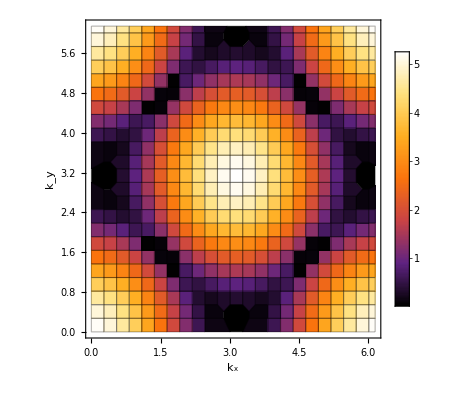

```mathematica
ListDensityPlot[exc,PlotRange->{0,6},ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotLegends->Automatic,ClippingStyle->Automatic]
```

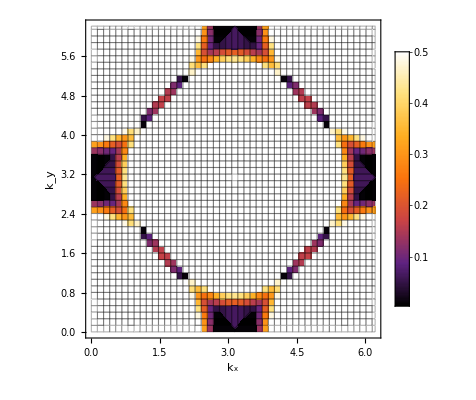
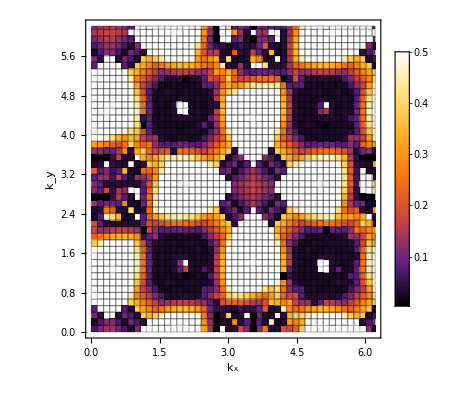

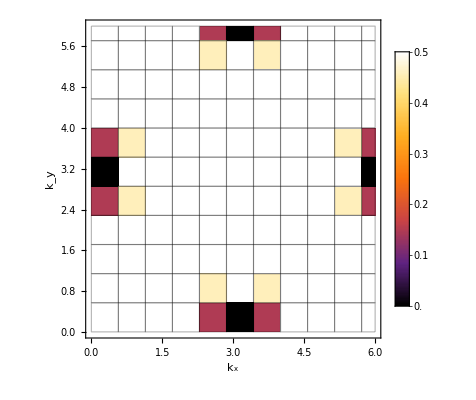
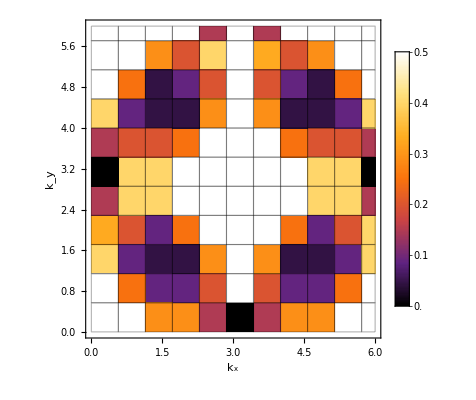

```mathematica
ListDensityPlot[exc,PlotRange->{0,0.5},ColorFunction->"SunsetColors",Mesh->All,InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"k_x","k_y"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotLegends->Automatic,ClippingStyle->Automatic]
```

-Graphics-

```mathematica
|
```

```mathematica
exc[[1;;50]]
```

{{(3 π)/47,(41 π)/47,0.00295437},{(3 π)/47,(53 π)/47,0.00295437},{(41 π)/47,(3 π)/47,0.00295437},{(41 π)/47,(91 π)/47,0.00295437},{(53 π)/47,(3 π)/47,0.00295437},{(53 π)/47,(91 π)/47,0.00295437},{(91 π)/47,(41 π)/47,0.00295437},{(91 π)/47,(53 π)/47,0.00295437},{(5 π)/47,(41 π)/47,0.00680595},{(5 π)/47,(53 π)/47,0.00680595},{(41 π)/47,(5 π)/47,0.00680595},{(41 π)/47,(89 π)/47,0.00680595},{(53 π)/47,(5 π)/47,0.00680595},{(53 π)/47,(89 π)/47,0.00680595},{(89 π)/47,(41 π)/47,0.00680595},{(89 π)/47,(53 π)/47,0.00680595},{π/47,(41 π)/47,0.00687323},{π/47,(53 π)/47,0.00687323},{(41 π)/47,π/47,0.00687323},{(41 π)/47,(93 π)/47,0.00687323},{(53 π)/47,π/47,0.00687323},{(53 π)/47,(93 π)/47,0.00687323},{(93 π)/47,(41 π)/47,0.00687323},{(93 π)/47,(53 π)/47,0.00687323},{(17 π)/47,(31 π)/47,0.00916144},{(17 π)/47,(63 π)/47,0.00916144},{(31 π)/47,(17 π)/47,0.00916144},{(31 π)/47,(77 π)/47,0.00916144},{(63 π)/47,(17 π)/47,0.00916144},{(63 π)/47,(77 π)/47,0.00916144},{(77 π)/47,(31 π)/47,0.00916144},{(77 π)/47,(63 π)/47,0.00916144},{(7 π)/47,(41 π)/47,0.0468948},{(7 π)/47,(53 π)/47,0.0468948},{(41 π)/47,(7 π)/47,0.0468948},{(41 π)/47,(87 π)/47,0.0468948},{(53 π)/47,(7 π)/47,0.0468948},{(53 π)/47,(87 π)/47,0.0468948},{(87 π)/47,(41 π)/47,0.0468948},{(87 π)/47,(53 π)/47,0.0468948},{(7 π)/47,(43 π)/47,0.0478114},{(7 π)/47,(51 π)/47,0.0478114},{(43 π)/47,(7 π)/47,0.0478114},{(43 π)/47,(87 π)/47,0.0478114},{(51 π)/47,(7 π)/47,0.0478114},{(51 π)/47,(87 π)/47,0.0478114},{(87 π)/47,(43 π)/47,0.0478114},{(87 π)/47,(51 π)/47,0.0478114},{(17 π)/47,(29 π)/47,0.0483266},{(17 π)/47,(65 π)/47,0.0483266}}

```mathematica
exc[[1;;50]]
```

{{(3 π)/47,(41 π)/47,0.00295437},{(3 π)/47,(53 π)/47,0.00295437},{(41 π)/47,(3 π)/47,0.00295437},{(41 π)/47,(91 π)/47,0.00295437},{(53 π)/47,(3 π)/47,0.00295437},{(91 π)/47,(41 π)/47,0.00295437},{(91 π)/47,(53 π)/47,0.00295437},{(5 π)/47,(41 π)/47,0.00680595},{(5 π)/47,(53 π)/47,0.00680595},{(41 π)/47,(5 π)/47,0.00680595},{(41 π)/47,(89 π)/47,0.00680595},{(53 π)/47,(5 π)/47,0.00680595},{(53 π)/47,(89 π)/47,0.00680595},{(89 π)/47,(41 π)/47,0.00680595},{(89 π)/47,(53 π)/47,0.00680595},{π/47,(41 π)/47,0.00687323},{π/47,(53 π)/47,0.00687323},{(41 π)/47,π/47,0.00687323},{(41 π)/47,(93 π)/47,0.00687323},{(53 π)/47,π/47,0.00687323},{(53 π)/47,(93 π)/47,0.00687323},{(93 π)/47,(41 π)/47,0.00687323},{(93 π)/47,(53 π)/47,0.00687323},{(17 π)/47,(31 π)/47,0.00916144},{(17 π)/47,(63 π)/47,0.00916144},{(31 π)/47,(17 π)/47,0.00916144},{(31 π)/47,(77 π)/47,0.00916144},{(63 π)/47,(17 π)/47,0.00916144},{(63 π)/47,(77 π)/47,0.00916144},{(77 π)/47,(31 π)/47,0.00916144},{(77 π)/47,(63 π)/47,0.00916144},{(25 π)/47,(13 π)/47,0.0219171},{(25 π)/47,(25 π)/47,0.0219171},{(31 π)/47,(13 π)/47,0.0219171},{(31 π)/47,(25 π)/47,0.0219171},{(69 π)/47,(63 π)/47,0.0219171},{(69 π)/47,(69 π)/47,0.0219171},{(81 π)/47,(69 π)/47,0.0219171},{(23 π)/47,(13 π)/47,0.0257687},{(23 π)/47,(25 π)/47,0.0257687},{(33 π)/47,(13 π)/47,0.0257687},{(33 π)/47,(25 π)/47,0.0257687},{(69 π)/47,(61 π)/47,0.0257687},{(69 π)/47,(71 π)/47,0.0257687},{(81 π)/47,(61 π)/47,0.0257687},{(81 π)/47,(71 π)/47,0.0257687},{(27 π)/47,(13 π)/47,0.025836},{(27 π)/47,(25 π)/47,0.025836},{(29 π)/47,(13 π)/47,0.025836},{(29 π)/47,(25 π)/47,0.025836}}

```mathematica
data[[1;;L^2]]
```

{{-π,-π,-2.8078},{0,0,-2.8078},{0,-π/6,-2.64759},{0,π/6,-2.64759},{-π,-(5 π)/6,-2.64759},{-π,(5 π)/6,-2.64759},{-(5 π)/6,-π,-2.64759},{-π/6,0,-2.64759},{π/6,0,-2.64759},{(5 π)/6,-π,-2.64759},{-(5 π)/6,-(5 π)/6,-2.47311},{-(5 π)/6,(5 π)/6,-2.47311},{-π/6,-π/6,-2.47311},{-π/6,π/6,-2.47311},{π/6,-π/6,-2.47311},{π/6,π/6,-2.47311},{(5 π)/6,-(5 π)/6,-2.47311},{(5 π)/6,(5 π)/6,-2.47311},{0,-π/3,-2.2104},{0,π/3,-2.2104},{-π,-(2 π)/3,-2.2104},{-π,(2 π)/3,-2.2104},{-(2 π)/3,-π,-2.2104},{-π/3,0,-2.2104},{π/3,0,-2.2104},{(2 π)/3,-π,-2.2104},{-(5 π)/6,-(2 π)/3,-1.99706},{-(5 π)/6,(2 π)/3,-1.99706},{-(2 π)/3,-(5 π)/6,-1.99706},{-(2 π)/3,(5 π)/6,-1.99706},{-π/3,-π/6,-1.99706},{-π/3,π/6,-1.99706},{-π/6,-π/3,-1.99706},{-π/6,π/3,-1.99706},{π/6,-π/3,-1.99706},{π/6,π/3,-1.99706},{π/3,-π/6,-1.99706},{π/3,π/6,-1.99706},{(2 π)/3,-(5 π)/6,-1.99706},{(2 π)/3,(5 π)/6,-1.99706},{(5 π)/6,-(2 π)/3,-1.99706},{(5 π)/6,(2 π)/3,-1.99706},{0,-π/2,-1.61556},{0,π/2,-1.61556},{-π,-π/2,-1.61556},{-π,π/2,-1.61556},{-π/2,0,-1.61556},{-π/2,-π,-1.61556},{π/2,0,-1.61556},{π/2,-π,-1.61556},{-π/3,-π/3,-1.41556},{-π/3,π/3,-1.41556},{π/3,-π/3,-1.41556},{π/3,π/3,-1.41556},{-(2 π)/3,-(2 π)/3,-1.41556},{-(2 π)/3,(2 π)/3,-1.41556},{(2 π)/3,-(2 π)/3,-1.41556},{(2 π)/3,(2 π)/3,-1.41556},{-(5 π)/6,-π/2,-1.35},{-(5 π)/6,π/2,-1.35},{-π/2,-(5 π)/6,-1.35},{-π/2,-π/6,-1.35},{-π/2,π/6,-1.35},{-π/2,(5 π)/6,-1.35},{-π/6,-π/2,-1.35},{-π/6,π/2,-1.35},{π/6,-π/2,-1.35},{π/6,π/2,-1.35},{π/2,-(5 π)/6,-1.35},{π/2,-π/6,-1.35},{π/2,π/6,-1.35},{π/2,(5 π)/6,-1.35},{(5 π)/6,-π/2,-1.35},{(5 π)/6,π/2,-1.35},{0,-(2 π)/3,-1.03078},{0,(2 π)/3,-1.03078},{-π,-π/3,-1.03078},{-π,π/3,-1.03078},{-(2 π)/3,0,-1.03078},{-π/3,-π,-1.03078},{π/3,-π,-1.03078},{(2 π)/3,0,-1.03078},{-(5 π)/6,-π/3,-0.719972},{-(5 π)/6,π/3,-0.719972},{-(2 π)/3,-π/6,-0.719972},{-(2 π)/3,π/6,-0.719972},{-π/3,-(5 π)/6,-0.719972},{-π/3,(5 π)/6,-0.719972},{-π/6,-(2 π)/3,-0.719972},{-π/6,(2 π)/3,-0.719972},{π/6,-(2 π)/3,-0.719972},{π/6,(2 π)/3,-0.719972},{π/3,-(5 π)/6,-0.719972},{π/3,(5 π)/6,-0.719972},{(2 π)/3,-π/6,-0.719972},{(2 π)/3,π/6,-0.719972},{(5 π)/6,-π/3,-0.719972},{(5 π)/6,π/3,-0.719972},{0,-(5 π)/6,-0.659286},{0,(5 π)/6,-0.659286},{-π,-π/6,-0.659286},{-π,π/6,-0.659286},{-(5 π)/6,0,-0.659286},{-π/6,-π,-0.659286},{π/6,-π,-0.659286},{(5 π)/6,0,-0.659286},{0,-π,-0.65},{-π,0,-0.65},{-(2 π)/3,-π/2,-0.630776},{-(2 π)/3,π/2,-0.630776},{-π/2,-(2 π)/3,-0.630776},{-π/2,-π/3,-0.630776},{-π/2,π/3,-0.630776},{-π/2,(2 π)/3,-0.630776},{-π/3,-π/2,-0.630776},{-π/3,π/2,-0.630776},{π/3,-π/2,-0.630776},{π/3,π/2,-0.630776},{π/2,-(2 π)/3,-0.630776},{π/2,-π/3,-0.630776},{π/2,π/3,-0.630776},{π/2,(2 π)/3,-0.630776},{(2 π)/3,-π/2,-0.630776},{(2 π)/3,π/2,-0.630776},{-(5 π)/6,-π/6,-0.45},{-(5 π)/6,π/6,-0.45},{-π/6,-(5 π)/6,-0.45},{-π/6,(5 π)/6,-0.45},{π/6,-(5 π)/6,-0.45},{π/6,(5 π)/6,-0.45},{(5 π)/6,-π/6,-0.45},{(5 π)/6,π/6,-0.45},{0,-π,-0.15},{-π,0,-0.15},{-(2 π)/3,-π/3,-0.05},{-(2 π)/3,π/3,-0.05},{-π/3,-(2 π)/3,-0.05},{-π/3,(2 π)/3,-0.05},{π/3,-(2 π)/3,-0.05},{π/3,(2 π)/3,-0.05},{(2 π)/3,-π/3,-0.05},{(2 π)/3,π/3,-0.05},{-(5 π)/6,-π/6,0.05},{-(5 π)/6,π/6,0.05}}

```mathematica
data[[1;;L^2+2]]
```

{{-π,-π,-2.8078},{0,0,-2.8078},{0,-π/6,-2.64759},{0,π/6,-2.64759},{-π,-(5 π)/6,-2.64759},{-π,(5 π)/6,-2.64759},{-(5 π)/6,-π,-2.64759},{-π/6,0,-2.64759},{π/6,0,-2.64759},{(5 π)/6,-π,-2.64759},{-(5 π)/6,-(5 π)/6,-2.47311},{-(5 π)/6,(5 π)/6,-2.47311},{-π/6,-π/6,-2.47311},{-π/6,π/6,-2.47311},{π/6,-π/6,-2.47311},{π/6,π/6,-2.47311},{(5 π)/6,-(5 π)/6,-2.47311},{(5 π)/6,(5 π)/6,-2.47311},{0,-π/3,-2.2104},{0,π/3,-2.2104},{-π,-(2 π)/3,-2.2104},{-π,(2 π)/3,-2.2104},{-(2 π)/3,-π,-2.2104},{-π/3,0,-2.2104},{π/3,0,-2.2104},{(2 π)/3,-π,-2.2104},{-(5 π)/6,-(2 π)/3,-1.99706},{-(5 π)/6,(2 π)/3,-1.99706},{-(2 π)/3,-(5 π)/6,-1.99706},{-(2 π)/3,(5 π)/6,-1.99706},{-π/3,-π/6,-1.99706},{-π/3,π/6,-1.99706},{-π/6,-π/3,-1.99706},{-π/6,π/3,-1.99706},{π/6,-π/3,-1.99706},{π/6,π/3,-1.99706},{π/3,-π/6,-1.99706},{π/3,π/6,-1.99706},{(2 π)/3,-(5 π)/6,-1.99706},{(2 π)/3,(5 π)/6,-1.99706},{(5 π)/6,-(2 π)/3,-1.99706},{(5 π)/6,(2 π)/3,-1.99706},{0,-π/2,-1.61556},{0,π/2,-1.61556},{-π,-π/2,-1.61556},{-π,π/2,-1.61556},{-π/2,0,-1.61556},{-π/2,-π,-1.61556},{π/2,0,-1.61556},{π/2,-π,-1.61556},{-π/3,-π/3,-1.41556},{-π/3,π/3,-1.41556},{π/3,-π/3,-1.41556},{π/3,π/3,-1.41556},{-(2 π)/3,-(2 π)/3,-1.41556},{-(2 π)/3,(2 π)/3,-1.41556},{(2 π)/3,-(2 π)/3,-1.41556},{(2 π)/3,(2 π)/3,-1.41556},{-(5 π)/6,-π/2,-1.35},{-(5 π)/6,π/2,-1.35},{-π/2,-(5 π)/6,-1.35},{-π/2,-π/6,-1.35},{-π/2,π/6,-1.35},{-π/2,(5 π)/6,-1.35},{-π/6,-π/2,-1.35},{-π/6,π/2,-1.35},{π/6,-π/2,-1.35},{π/6,π/2,-1.35},{π/2,-(5 π)/6,-1.35},{π/2,-π/6,-1.35},{π/2,π/6,-1.35},{π/2,(5 π)/6,-1.35},{(5 π)/6,-π/2,-1.35},{(5 π)/6,π/2,-1.35},{0,-(2 π)/3,-1.03078},{0,(2 π)/3,-1.03078},{-π,-π/3,-1.03078},{-π,π/3,-1.03078},{-(2 π)/3,0,-1.03078},{-π/3,-π,-1.03078},{π/3,-π,-1.03078},{(2 π)/3,0,-1.03078},{-(5 π)/6,-π/3,-0.719972},{-(5 π)/6,π/3,-0.719972},{-(2 π)/3,-π/6,-0.719972},{-(2 π)/3,π/6,-0.719972},{-π/3,-(5 π)/6,-0.719972},{-π/3,(5 π)/6,-0.719972},{-π/6,-(2 π)/3,-0.719972},{-π/6,(2 π)/3,-0.719972},{π/6,-(2 π)/3,-0.719972},{π/6,(2 π)/3,-0.719972},{π/3,-(5 π)/6,-0.719972},{π/3,(5 π)/6,-0.719972},{(2 π)/3,-π/6,-0.719972},{(2 π)/3,π/6,-0.719972},{(5 π)/6,-π/3,-0.719972},{(5 π)/6,π/3,-0.719972},{0,-(5 π)/6,-0.659286},{0,(5 π)/6,-0.659286},{-π,-π/6,-0.659286},{-π,π/6,-0.659286},{-(5 π)/6,0,-0.659286},{-π/6,-π,-0.659286},{π/6,-π,-0.659286},{(5 π)/6,0,-0.659286},{0,-π,-0.65},{-π,0,-0.65},{-(2 π)/3,-π/2,-0.630776},{-(2 π)/3,π/2,-0.630776},{-π/2,-(2 π)/3,-0.630776},{-π/2,-π/3,-0.630776},{-π/2,π/3,-0.630776},{-π/2,(2 π)/3,-0.630776},{-π/3,-π/2,-0.630776},{-π/3,π/2,-0.630776},{π/3,-π/2,-0.630776},{π/3,π/2,-0.630776},{π/2,-(2 π)/3,-0.630776},{π/2,-π/3,-0.630776},{π/2,π/3,-0.630776},{π/2,(2 π)/3,-0.630776},{(2 π)/3,-π/2,-0.630776},{(2 π)/3,π/2,-0.630776},{-(5 π)/6,-π/6,-0.45},{-(5 π)/6,π/6,-0.45},{-π/6,-(5 π)/6,-0.45},{-π/6,(5 π)/6,-0.45},{π/6,-(5 π)/6,-0.45},{π/6,(5 π)/6,-0.45},{(5 π)/6,-π/6,-0.45},{(5 π)/6,π/6,-0.45},{0,-π,-0.15},{-π,0,-0.15},{-(2 π)/3,-π/3,-0.05},{-(2 π)/3,π/3,-0.05},{-π/3,-(2 π)/3,-0.05},{-π/3,(2 π)/3,-0.05},{π/3,-(2 π)/3,-0.05},{π/3,(2 π)/3,-0.05},{(2 π)/3,-π/3,-0.05},{(2 π)/3,π/3,-0.05},{-(5 π)/6,-π/6,0.05},{-(5 π)/6,π/6,0.05},{-π/6,-(5 π)/6,0.05},{-π/6,(5 π)/6,0.05}}

```mathematica
|
```

```mathematica
occupied1=data[[1;;L^2+1]];
empty1=Complement[data,occupied1];
exc=Flatten[ParallelTable[{Mod[Kx1-occupied1[[i]][[1]]+empty1[[j]][[1]]-Kx0,2π],Mod[Ky1-occupied1[[i]][[2]]+empty1[[j]][[2]]-Ky0,2π],En1-occupied1[[i]][[3]]+empty1[[j]][[3]]-En0}

,{i,L^2,L^2+1},{j,L^2+1-100,L^2-1}],1];
exc=SortBy[exc,Last];
exc[[1;;50]]
```

{{π/6,(5 π)/6,0.05},{π/6,(7 π)/6,0.05},{π/2,(11 π)/6,0.05},{(5 π)/6,π/6,0.05},{(5 π)/6,π/6,0.05},{(5 π)/6,(11 π)/6,0.05},{(5 π)/6,(11 π)/6,0.05},{(3 π)/2,(5 π)/6,0.05},{(3 π)/2,(7 π)/6,0.05},{(11 π)/6,(5 π)/6,0.05},{π/6,π,0.0736449},{π/2,0,0.0736449},{(5 π)/6,0,0.0736449},{(5 π)/6,0,0.0736449},{(3 π)/2,π,0.0736449},{(11 π)/6,π,0.0736449},{π/6,π/2,0.15},{π/6,(3 π)/2,0.15},{π/2,π/2,0.15},{π/2,(3 π)/2,0.15},{(7 π)/6,π/2,0.15},{(7 π)/6,(3 π)/2,0.15},{(3 π)/2,π/2,0.15},{(3 π)/2,(3 π)/2,0.15},{π/3,π/3,0.45},{π/3,(2 π)/3,0.45},{π/3,(4 π)/3,0.45},{π/3,(5 π)/3,0.45},{(2 π)/3,π/3,0.45},{(2 π)/3,(5 π)/3,0.45},{π,π/3,0.45},{π,(5 π)/3,0.45},{(4 π)/3,(2 π)/3,0.45},{(4 π)/3,(4 π)/3,0.45},{(5 π)/3,(2 π)/3,0.45},{(5 π)/3,(4 π)/3,0.45},{π/6,π/2,0.65},{π/6,(3 π)/2,0.65},{π/2,π/2,0.65},{π/2,(3 π)/2,0.65},{(7 π)/6,π/2,0.65},{(7 π)/6,(3 π)/2,0.65},{(3 π)/2,π/2,0.65},{(3 π)/2,(3 π)/2,0.65},{π/6,(2 π)/3,0.827152},{π/6,(4 π)/3,0.827152},{π/3,π/6,0.827152},{π/3,(5 π)/6,0.827152},{π/3,(7 π)/6,0.827152},{π/3,(11 π)/6,0.827152}}

```mathematica
occupied1=data[[1;;L^2+1]];
empty1=Complement[data,occupied1];
exc=Flatten[ParallelTable[{Mod[+empty1[[j]][[1]],2π],Mod[Ky1-occupied1[[j]][[2]]+empty1[[j]][[2]]-Ky0,2π],En1-occupied1[[i]][[3]]+empty1[[j]][[3]]-En0}

,{i,L^2+1,L^2+1},{j,L^2+1-100,L^2-1}],1];
exc=SortBy[exc,Last];
exc[[1;;50]]
```

{{π/6,0,0.05},{π/6,(5 π)/6,0.05},{(5 π)/6,0,0.05},{(5 π)/6,π/3,0.05},{(11 π)/6,π,0.05},{π/6,π/2,0.0736449},{(5 π)/6,π,0.0736449},{(11 π)/6,(4 π)/3,0.0736449},{π/2,π/6,0.15},{π/2,(7 π)/6,0.15},{(3 π)/2,π/3,0.15},{(3 π)/2,(2 π)/3,0.15},{π/3,(5 π)/6,0.45},{π/3,(5 π)/6,0.45},{(2 π)/3,(2 π)/3,0.45},{(2 π)/3,π,0.45},{(5 π)/3,(2 π)/3,0.45},{(5 π)/3,(2 π)/3,0.45},{π/2,π/6,0.65},{π/2,(4 π)/3,0.65},{(3 π)/2,π,0.65},{(3 π)/2,(5 π)/3,0.65},{π/6,(2 π)/3,0.827152},{π/6,(7 π)/6,0.827152},{π/3,π/6,0.827152},{π/3,π,0.827152},{(2 π)/3,π/6,0.827152},{(2 π)/3,(5 π)/6,0.827152},{(5 π)/6,(5 π)/6,0.827152},{(5 π)/6,(3 π)/2,0.827152},{(5 π)/3,π/6,0.827152},{(5 π)/3,(7 π)/6,0.827152},{(11 π)/6,(5 π)/6,0.827152},{(11 π)/6,π,0.827152},{π/3,π/3,1.03078},{(2 π)/3,(3 π)/2,1.03078},{(5 π)/3,(5 π)/3,1.03078},{π/3,π/3,1.43078},{π/3,(5 π)/3,1.43078},{π/2,0,1.43078},{π/2,π,1.43078},{π/2,(7 π)/6,1.43078},{π/2,(4 π)/3,1.43078},{(2 π)/3,π/6,1.43078},{(2 π)/3,π/2,1.43078},{(3 π)/2,π/2,1.43078},{(3 π)/2,(7 π)/6,1.43078},{(3 π)/2,(7 π)/6,1.43078},{(3 π)/2,(3 π)/2,1.43078},{(5 π)/3,π/2,1.43078}}